```mathematica
Manipulate[
Module[{θY,θm,V,R,h,step,rough},
θY:=ArcCos[fA*Cos[θA Degree]+(1-fA)*Cos[θB Degree]];(*Young contact angle*)
θm:=ArcCos[r*Cos[θY]];(*measured contact angle*)

V=0.05;
R:=(3^(1/3)*V^(1/3))/((2*π-3*π*Cos[θm]+π*Cos[θm]^3)^(1/3));
h:=R-R*Sin[π/2-θm];

(*step:=Interpolation[{{1,4},{1.1,0.5},{1.5,0.275},{1.7,0.1625},{1.9,0.05}},InterpolationOrder->1][r];*)
rough:=0.03*Rescale[r,{1,1.9}];

Show[
RegionPlot[x^2+(y+(R-h))^2<R^2,{x,-R,R},{y,0,1},PlotStyle->RGBColor[0.,0.62,0.72],PlotPoints->10,MaxRecursion->2],
Graphics[FilledCurve[{Line[Sort[Table[{0.5*i,RandomReal[{0,rough}]},{i,-1,1,0.05}]]],Line[{{0.5,-0.5},{-0.5,-0.5}}]}]],
(*Graphics[{GrayLevel[0.3],Table[Rectangle[{0.5*i,0},{0.5*(i+step/2),-0.02}],{i,-1,1,step}]}],*)
FrameStyle->Black,
LabelStyle->13,
FrameLabel->{Style["cm",17],Style["cm",17]},
PlotRange->{{-0.5,0.5},{0,0.7}},
PlotRangePadding->{None,0.02},
AspectRatio->0.5/0.7,
ImageSize->450,PlotLabel->{x^2+(y+(R-h))^2<R^2,R,h}]
],
Control[{{fA,0.25,"fraction of surface A"},0,1,0.01,Appearance->"Labeled"}],
Control[{{r,1,"roughness ratio"},1,1.9,0.1,Appearance->"Labeled"}],
Style["surface contact angles (degrees):",Bold],
Row[{
Control[{{θA,20,Subscript["θ","A"]},10,110,1,Appearance->"Labeled",ImageSize->Small}],
Control[{{θB,80,Subscript["θ","B"]},10,110,1,Appearance->"Labeled",ImageSize->Small}]
}]
]
```

```mathematica
Manipulate[
Module[{rough},
(*rough:=0.03*Rescale[r,{1,1.9}];
Graphics[{FilledCurve[{Line[Sort[Table[{0.5*i,RandomReal[{0,rough}]},{i,-1,1,0.05}]]],Line[{{0.5,-0.5},{-0.5,-0.5}}]}]},
AspectRatio->0.5/0.7,PlotRange->{{-0.5,0.5},{0,0.7}},PlotRangePadding->{None,0.01},ImageSize->450,Frame->True]*)

(*rough:=1.1-Rescale[r,{0.9,1.9}];*)
rough=1;

Graphics[{
(*FilledCurve[{
Line[Sort[Table[{0.5*i,RandomReal[{0,0.02}]},{i,-1,1,rough}]]],
Line[{{0.5,-0.5},{-0.5,-0.5}}]
}]*)
PointSize[0.02],Table[Point[{0.5*i,RandomReal[{0,0.1}]}],{i,-1,1,2}],

},
AspectRatio->0.5/0.7,PlotRange->{{-0.5,0.5},{0,0.7}},PlotRangePadding->{None,0.01},ImageSize->450,Frame->True]

],
{{r,1.9,"roughness"},1,1.9,0.1,Appearance->"Labeled"}]
```

```mathematica
Manipulate[
Module[{opt,R,h,rough},
opt=Sequence[FrameStyle->Black,LabelStyle->13,FrameLabel->{Style["cm",17],Style["cm",17]},PlotRange->{{-0.5,0.5},{0,0.7}},PlotRangePadding->{None,0.02},AspectRatio->0.5/0.7,ImageSize->450];

R=0.2351;
h=0.3879;

(*rough=0.1*(1-Rescale[r,{0.9,1.9}]);*)
(*rough=0.1*Rescale[r,{0.9,1.9}];*)
rough=0.1*(1-Rescale[r,{1,2}]);

Grid[{{
Show[
RegionPlot[x^2+(y-0.15)^2<0.055,{x,-R,R},{y,0,1},PlotStyle->RGBColor[0.,0.62,0.72]],
Graphics[{
GrayLevel[0.3],
(*FilledCurve[{
Line[Sort@Table[{0.5*i,RandomReal[{0,0.025}]},{i,-1,1+rough,rough}]],
Line[{{0.5,-0.5},{-0.5,-0.5}}]
}]*)
If[r==1,
Rectangle[{-0.5,-0.5},{0.5,0.025}],
FilledCurve[{
Line[Sort@Table[{0.5*i,RandomReal[{0,0.025}]},{i,-1,1+rough,rough}]],
Line[{{0.5,-0.5},{-0.5,-0.5}}]
}]
]
}],
Evaluate@opt,PlotLabel->rough],
Show[
RegionPlot[x^2+(y-0.15)^2<0.055,{x,-R,R},{y,0,1},PlotStyle->RGBColor[0.,0.62,0.72]],
Graphics[{
GrayLevel[0.3],FilledCurve[{
Line[Sort@Table[{0.5*i,RandomReal[{0,0.025}]},{i,-1,1+step,step}]],
Line[{{0.5,-0.5},{-0.5,-0.5}}]
}]
}],
Evaluate@opt,PlotLabel->step]
}}]

],
Control[{{step,0.01,"step"},0.01,0.2,0.01,Appearance->"Labeled"}],
Control[{{r,1,"roughness"},1,1.9,0.1,Appearance->"Labeled"}]
]
```

```mathematica
{{1.9,0.01},{1.1,
```

```mathematica
s
```

```mathematica
Sort@Table[{0.5*i,RandomReal[{0,0.01}]},{i,-1,1,0.1}]
```

{{-0.5,0.00939968},{-0.45,0.000163283},{-0.4,0.00442492},{-0.35,0.00376614},{-0.3,0.00832681},{-0.25,0.00413556},{-0.2,0.000293938},{-0.15,0.00325047},{-0.1,0.000915957},{-0.05,0.000288469},{0.,0.0095838},{0.05,0.00570026},{0.1,0.00446459},{0.15,0.00787719},{0.2,0.00728527},{0.25,0.00435018},{0.3,0.0077375},{0.35,0.0061899},{0.4,0.00771552},{0.45,0.00547503},{0.5,0.00604755}}

```mathematica
Length[Range[1,1.9,0.1]]
```

10

```mathematica
Length[Range[0.01,0.1,0.01]]
```

10

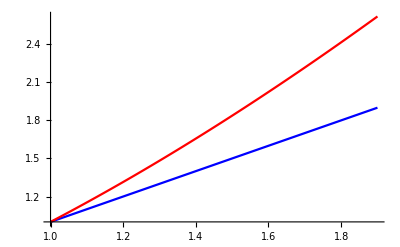

```mathematica
Plot[{r,r^(3/2)},{r,1,1.9},PlotStyle->{Blue,Red}]
```

```mathematica
{{1.1,0.09},{1.2,0.08},{1.3,0.07},{1.4,0.06},{1.5,0.05},{1.6,0.04},{1.7,0.03},{1.8,0.02},{1.9,0.01}}
Table[{r,0.1*Rescale[r,{1,2}]},{r,1.1,1.9,0.1}]
Table[{r,0.1*(1-Rescale[r,{1,2}])},{r,1.1,1.9,0.1}]
```

{{1.1,0.09},{1.2,0.08},{1.3,0.07},{1.4,0.06},{1.5,0.05},{1.6,0.04},{1.7,0.03},{1.8,0.02},{1.9,0.01}}

{{1.1,0.01},{1.2,0.02},{1.3,0.03},{1.4,0.04},{1.5,0.05},{1.6,0.06},{1.7,0.07},{1.8,0.08},{1.9,0.09}}

{{1.1,0.09},{1.2,0.08},{1.3,0.07},{1.4,0.06},{1.5,0.05},{1.6,0.04},{1.7,0.03},{1.8,0.02},{1.9,0.01}}